```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
threshold = 1;
δ=0.05;
T=30;C0=1;C1=0.7;τ2=0.4;τ1=τ2-δ;τ3=1-δ;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=1000;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
```

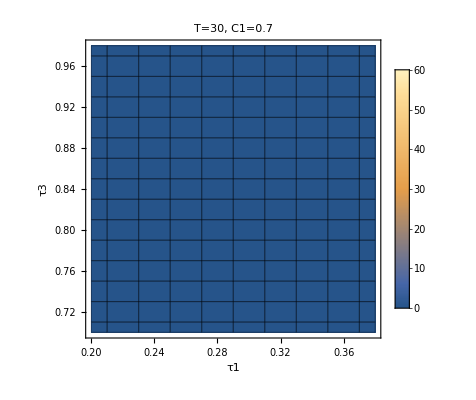

FHN_30_C1_0.7.png

```mathematica
(*Solving FHN*)
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;

simulation={};
τ2=0.4;τ4=1;
fRateHH={};
Do[Do[
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.2Min[τ2-τ1,1-τ3]T];
peaksHH = FindPeaks[Table[V[t],{t,0,maxtime,1}],0,0,threshold];
countHH=Length[peaksHH];
pointHH = {τ1,τ3,N[countHH/maxtime *1000]};
fRateHH = Append[fRateHH,pointHH];
,{τ1,0.2,0.399,0.02}],{τ3,0.7,0.999,0.02}];
extract=fRateHH[[All,{1,2,3}]];
g1= ListDensityPlot[extract,Mesh->All,InterpolationOrder->0,PlotLegends->BarLegend[{Automatic,{0,60}}],PlotLegends->Automatic,PlotRange->{Full,Full,{0,60}},PlotRangeClipping->False,
PlotLabel->StringJoin["T=",ToString[T],", C1=",ToString[C1]],FrameLabel->{"τ1","τ3"}]

(*ColorFunction->(ColorData["SunsetColors"][0.9(1-#/60)+0.07]&),ColorFunctionScaling->False,*)
filename=StringJoin["FHN_",ToString[T],"_C1_",ToString[C1],".png"];
Export[filename,g1]
```

```mathematica
FrHH=fRateHH[[All,{1,2,3}]]; 
plot1=ListDensityPlot[FrHH,Mesh->All,InterpolationOrder->0,PlotRange->{Full,Full,Full},PlotRangeClipping->False,PlotLegends->Automatic,ColorFunction->(ColorData["SunsetColors"][(1-#)]&),ColorFunctionScaling->True, PlotLabel->"HH"];
FrHHs=fRateHHs[[All,{1,2,3}]]; 
plot2=ListDensityPlot[FrHHs,Mesh->All,InterpolationOrder->0,PlotRange->{Full,Full,Full},PlotRangeClipping->False,PlotLegends->Automatic,ColorFunction->(ColorData["SunsetColors"][(1-#)]&),ColorFunctionScaling->True, PlotLabel->"HH smoothed"];

GraphicsRow[{plot1 , plot2}, Spacings->0]

(*Export["dataFrHH.csv",FrHH]*)
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

-Graphics-